-Graphics3D-

-Graphics-

-Graphics3D-

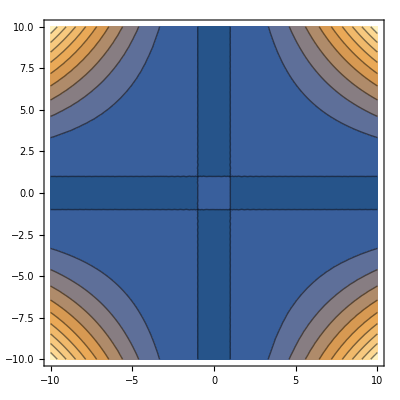

```mathematica
(*3D plot and contour plot*)
Plot3D[Sin[x]-Sin[y],{x,-10,10},{y,-10,10}]
ContourPlot[Sin[x]-Sin[y],{x,-10,10},{y,-10,10}]
(*Plot3D[Sin[x]-Sin[y],{x,-Pi,Pi},{y,-Pi,Pi}]
ContourPlot[Sin[x]-Sin[y],{x,-Pi,Pi},{y,-Pi,Pi}]*)
Plot3D[(1-x^2)(1-y^2),{x,-10,10},{y,-10,10}, PlotRange->All]
ContourPlot[(1-x^2)(1-y^2),{x,-10,10},{y,-10,10}, PlotRange->All]
```

-Graphics3D-

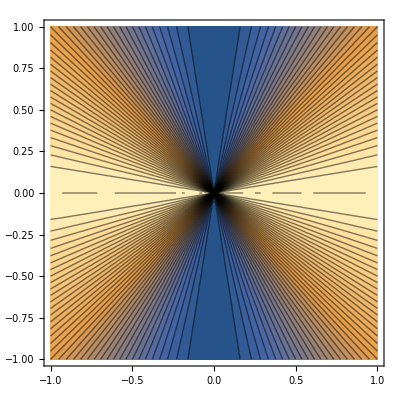

Indeterminate

-Graphics3D-

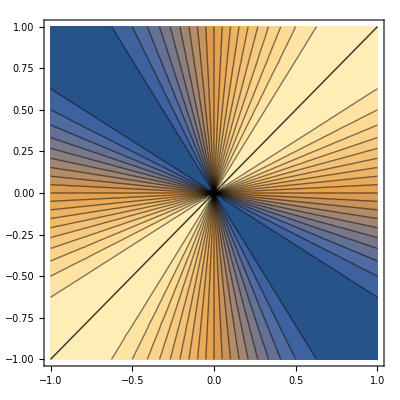

Indeterminate

```mathematica
(*Jump discontinuity*)
Plot3D[(x^2-y^2)/(x^2+y^2),{x,-1,1},{y,-1,1}, PlotRange->All]
ContourPlot[(x^2-y^2)/(x^2+y^2),{x,-1,1},{y,-1,1},Contours->Function[{min,max},Range[min,max,0.05]]]
Limit[(x^2-y^2)/(x^2+y^2),{x,y}->{0,0}]
Plot3D[(x y)/(x^2+y^2),{x,-1,1},{y,-1,1}, PlotRange->All]
ContourPlot[(x y)/(x^2+y^2),{x,-1,1},{y,-1,1},Contours->Function[{min,max},Range[min,max,0.05]]]
Limit[(x y)/(x^2+y^2),{x,y}->{0,0}]
```

```mathematica
(*Removable discontinuity*)
```

-Graphics3D-

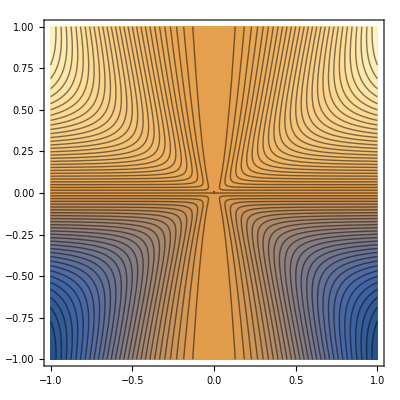

0

```mathematica
Plot3D[(3 x^2 y)/(x^2+y^2),{x,-1,1},{y,-1,1}, PlotRange->All]
ContourPlot[(3 x^2 y)/(x^2+y^2),{x,-1,1},{y,-1,1},Contours->Function[{min,max},Range[min,max,0.05]]]
Limit[(3 x^2 y)/(x^2+y^2),{x,y}->{0,0}]
```

-Graphics3D-

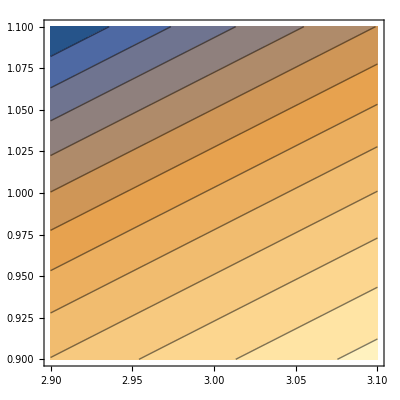

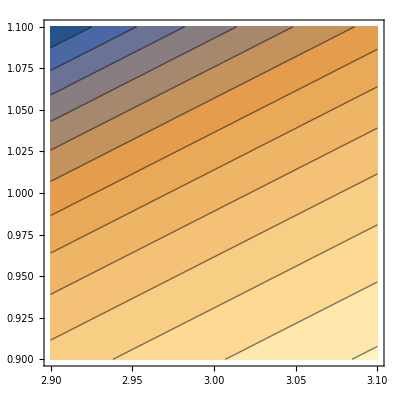

-Graphics-

-Graphics-

```mathematica
(*Linearization*)
f[x_,y_]:=Log[x-2y]
Subscript[f, 1][x_,y_]:=D[f[s,t],s]/.{s->x, t->y}
Subscript[f, 2][x_,y_]:=D[f[s,t],t]/.{s->x, t->y}
Show[{
Plot3D[f[x,y],{x,2,4},{y,0,2},PlotRange->All, PlotStyle->Red],Plot3D[f[3,1]+Subscript[f, 1][x,y]*(x-3)+Subscript[f, 2][x,y]*(y-1),{x,2,4},{y,0,1.5},PlotRange->All]
}]
(*Plot3D[f[3,1]+D[f[x,y],x]*x+D[f[x,y],y]*y,{x,2.9,3.1},{y,0.9,1.1},PlotRange->All]*)
ContourPlot[f[x,y],{x,2.9,3.1},{y,0.9,1.1},Contours->Function[{min,max},Range[min,max,0.05]]]
ContourPlot[f[3,1]+Subscript[f, 1][x,y]*(x-3)+Subscript[f, 2][x,y]*(y-1),{x,2.9,3.1},{y,0.9,1.1},Contours->Function[{min,max},Range[min,max,0.05]]]
```

```mathematica
(*Newton's law*)
myNorm[r_]:=Sqrt[Sum[r⟦k⟧^2,{k,1,Length[r]}]]
F[r_]:= (G  m M)/myNorm[r]
GradF[r_]:=Grad[F[r],r]
F[{x,y,z}]
GradF[{x,y,z}]
```

(G m M)/(√(x^2+y^2+z^2))

{-(G m M x)/((x^2+y^2+z^2)^(3/2)),-(G m M y)/((x^2+y^2+z^2)^(3/2)),-(G m M z)/((x^2+y^2+z^2)^(3/2))}

```mathematica
(*Chain rule*)
u[x_,y_,t_]:=x Exp[y t]
Simplify@Grad[u[α^2β,β^2γ,γ^2α],{α,β,γ}]
```

{ⅇ^(α β^2 γ^3) α β (2+α β^2 γ^3),ⅇ^(α β^2 γ^3) α^2 (1+2 α β^2 γ^3),3 ⅇ^(α β^2 γ^3) α^3 β^3 γ^2}

```mathematica
(*Chain rule*)
w[x_,y_,z_]:=x y + y z + z x
Simplify@Grad[u[r Cos[θ],r Sin[θ],r θ],{r, θ}]
Simplify@Grad[u[r Cos[θ],r Sin[θ],r θ],{r, θ}]/.{r->2,θ->Pi/2}
```

{ⅇ^(r^2 θ Sin[θ]) Cos[θ] (1+2 r^2 θ Sin[θ]),ⅇ^(r^2 θ Sin[θ]) r (r^2 θ Cos[θ]^2-Sin[θ]+r^2 Cos[θ] Sin[θ])}

{0,-2 ⅇ^(2 π)}

```mathematica
(*Directional derivative*)
f[x_,y_]:=x^2 y
direction={1,2};
(Grad[f[x,y],{x,y}]/.{x->3,y->2}).direction
```

30